```mathematica
SetDirectory[NotebookDirectory[]];
<<"chiralMechanics.m"
<<"chiralGraph.m"
```

Cases for the SI of the article model-free:
1. Single domain
2. FM domain wall
3. SSS domain wall

#### General parameters

```mathematica
unitcellLength=60.;(*This is the distance between two consecutive pivots in mm*)
radius=18. √2;
```

## Single domain

```mathematica
nRotors=31;(*30;*)
angleListSingleDomain=N@((-1)^#)3π/4&/@Range[nRotors];
```

```mathematica
(*Model dependent part*)
Clear[keysBeadsUC,pairKeysUC,posBeadsUC,identityUC,translationOp,posPivotsUC];
{keysBeadsUC[i_],pairKeysUC[i_],identityUC,posBeadsUC,translationOp[i_],posPivotsUC}=Module[{keysBeads,posBeads,pairKeys,identity,l={i},pVec1,pVec2,transOp,posPivots,recBasis},
Clear[a,b];
(*definition of beads and connectivity*)
keysBeads=#@@l&/@{a,b};
pairKeys={{a@@l,b@@l},{b@@l,a@@(l+1)}};

(*primitive vectors and positions*)
pVec1=2{unitcellLength,0};
transOp={pVec1}(i-1);
posPivots={{0,0},pVec1/2};
posBeads=Table[posPivots[[i]]+radius AngleVector[(-1)^i 3π/4],{i,1,2}];
identity={1,1};


{keysBeads,pairKeys,identity,posBeads,transOp,posPivots}
];
```

```mathematica
{keysBeads,pairKeysBeads,identity,posBeads,posPivots}=tesselate[{Ceiling[nRotors/2]},keysBeadsUC,pairKeysUC,identityUC,posBeadsUC,translationOp,posPivotsUC];
```

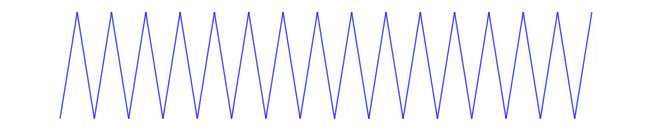

```mathematica
beadAndSpringGraphic2D[{keysBeads,pairKeysBeads,identity,posBeads,posPivots}]
```

```mathematica
graphBeads=eqSystem[keysBeads,pairKeysBeads,AssociationThread[keysBeads,posBeads]];
graphPert=pertSystem[graphBeads,AssociationThread[keysBeads,identity],AssociationThread[keysBeads,posBeads],AssociationThread[keysBeads,posPivots]];
```

### Periodic parameters

```mathematica
Normal[WeightedAdjacencyMatrix[graphPert]][[6]]
```

{0,0,0,0,0.970143,0,0.242536,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
q1F[θ_,r_,a_]:=r Sin[θ](a+2r Sin[θ])/(√(a^2+4 r^2 Sin[θ]^2));
q2F[θ_,r_,a_]:=r Sin[θ](a-2r Sin[θ])/(√(a^2+4 r^2 Sin[θ]^2));
```

```mathematica
q1F[45Degree,radius,unitcellLength]/radius
q2F[45Degree,radius,unitcellLength]/radius
```

0.970143

0.242536

#### Spectrum

```mathematica
h[k_]=With[{t1=q1F[45Degree,radius,unitcellLength]/radius,t2=q2F[45Degree,radius,unitcellLength]/radius},({{0, t1+t2 ⅇ^(ⅈ k)}, {t1+t2 ⅇ^(-ⅈ k), 0}})];
```

```mathematica
Eigenvalues[h[k]]
```

{-1. ⅇ^(-ⅈ k) √(0.235294 ⅇ^(ⅈ k)+1. ⅇ^(2 ⅈ k)+0.235294 ⅇ^(3 ⅈ k)),1. ⅇ^(-ⅈ k) √(0.235294 ⅇ^(ⅈ k)+1. ⅇ^(2 ⅈ k)+0.235294 ⅇ^(3 ⅈ k))}

```mathematica
q2F[45Degree,radius,unitcellLength]/q1F[45Degree,radius,unitcellLength]
```

0.25

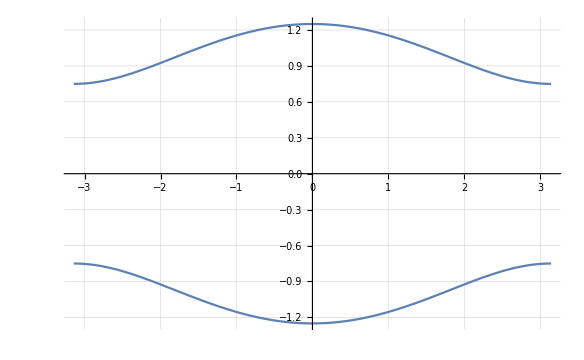

```mathematica
Plot[{Sqrt[t1^2+t2^2+2 t1 t2 Cos[k]]/t1,-Sqrt[t1^2+t2^2+2 t1 t2 Cos[k]]/t1}/.{t1->q1F[45Degree,radius,unitcellLength],t2->q2F[45Degree,radius,unitcellLength]},{k,-π,π},GridLines->Automatic]
```

### Finite system

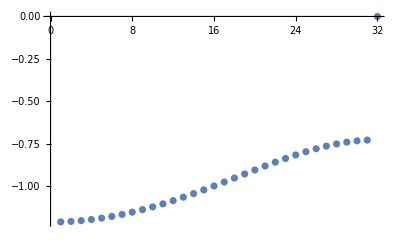

```mathematica
{{negEval,negEvec},{zmEval,zmEvec}}=negativeAndZMspectrum[Normal[WeightedAdjacencyMatrix[graphPert]],0.01];
{projA,projB}={projAList[#],projBList[#]}&@graphPert;
ListPlot[negEval~Join~zmEval]
```

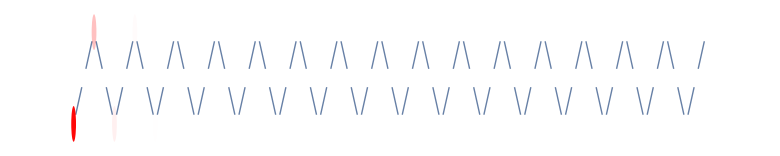

```mathematica
highlightGraph[Graph[graphPert,VertexSize->0.4],Total[zmEvec^2]^(1/2),0]
```

```mathematica
{localBasis,accuracyList}=localizedBasisPencilMatrix[graphPert,negEvec,0.9];
```

#### Visualization of Wannier functions

```mathematica
positions=positionList[graphPert];
```

```mathematica
nWannier=16;
data={positions[[All,1]],localBasis[[nWannier]]}ᵀ;
```

```mathematica
colorList=If[#==-1,Blue,Red]&/@chiralList[graphPert];
```

```mathematica
positions
```

{{12.,0.},{-18.,-18.},{42.,18.},{72.,0.},{102.,-18.},{132.,0.},{162.,18.},{192.,0.},{222.,-18.},{252.,0.},{282.,18.},{312.,0.},{342.,-18.},{372.,0.},{402.,18.},{432.,0.},{462.,-18.},{492.,0.},{522.,18.},{552.,0.},{582.,-18.},{612.,0.},{642.,18.},{672.,0.},{702.,-18.},{732.,0.},{762.,18.},{792.,0.},{822.,-18.},{852.,0.},{882.,18.},{912.,0.},{942.,-18.},{972.,0.},{1002.,18.},{1032.,0.},{1062.,-18.},{1092.,0.},{1122.,18.},{1152.,0.},{1182.,-18.},{1212.,0.},{1242.,18.},{1272.,0.},{1302.,-18.},{1332.,0.},{1362.,18.},{1392.,0.},{1422.,-18.},{1452.,0.},{1482.,18.},{1512.,0.},{1542.,-18.},{1572.,0.},{1602.,18.},{1632.,0.},{1662.,-18.},{1692.,0.},{1722.,18.},{1752.,0.},{1782.,-18.},{1812.,0.},{1842.,18.}}

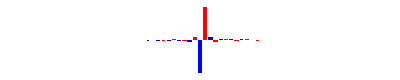

```mathematica
width=20;
amplificationFactor=200;
Graphics[MapThread[{#2,Rectangle[{#[[1]]-width/2,0},{#[[1]]+width/2,amplificationFactor#[[2]]}]}&,{data,colorList}]]
```

```mathematica
localBasis[[7]]//Dimensions
```

{63}

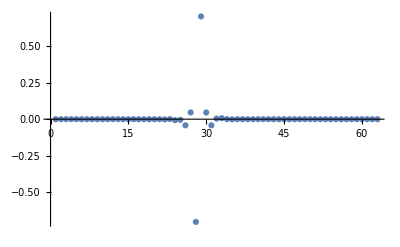

{27,2}

```mathematica
ListPlot[localBasis[[14]],PlotRange->All]
```

```mathematica
listBlue=ToExpression@;
listRed=ToExpression@;
balanceRedColorMap=Blend[Reverse[RGBColor[#]&/@listRed],#]&;
balanceBlueColorMap=Blend[Reverse[RGBColor[#]&/@listBlue],#]&;
```

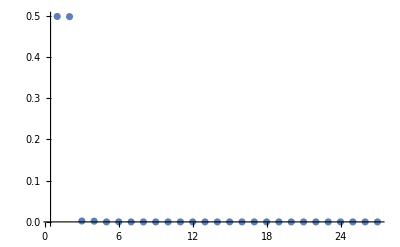

```mathematica
ListPlot[localBasis[[1]]^2,PlotRange->All]
```

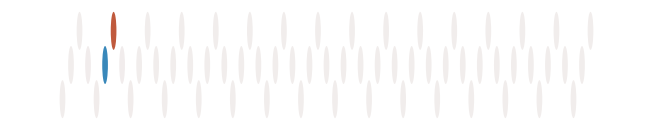

```mathematica
n=3;
Show[
Graphics[Pick[MapThread[{balanceRedColorMap[#1],Disk[#2,10]}&,{localBasis[[n]]^2,positions}],projA,1]],
Graphics[Pick[MapThread[{balanceBlueColorMap[#1],Disk[#2,10]}&,{localBasis[[n]]^2,positions}],projB,1]]
]
```

#### Chiral polarization field

```mathematica
positions=positionList[graphPert];
chiral=chiralList[graphPert];
```

```mathematica
momentsList=Quiet@Map[With[{norm2=(#*.#)},
{
Sqrt[norm2],
(#*.(chiral#))/norm2,
1/norm2(#*.(positions[[All,1]]#)),
1/norm2(#*.(positions[[All,2]]#)),
1/norm2(#*.(chiral positions[[All,1]]#)),
1/norm2(#*.(chiral positions[[All,2]]#))
}]&,localBasis];
```

```mathematica
fieldData=Map[{#[[3]],#[[4]],2(#[[5]]-#[[2]]#[[3]]),2(#[[6]]-#[[2]]#[[4]])}&,momentsList];
```

```mathematica
fcolor=GrayLevel[(35-#)/35]&;
barl=BarLegend[{fcolor[#]&,{0,40}},LegendLabel->"Norm",LabelStyle->Directive[Black,FontSize->14]];
primitivesList=Map[Module[{center={#1[[1]],#1[[2]]},pol={#1[[3]],#1[[4]]},unitvector,norm,circleRadius=15},
norm=Norm@pol;
unitvector=Normalize[pol];
{fcolor[norm],Thickness[0.005],Arrowheads[.01],Arrow[{center-unitvector circleRadius,center+unitvector circleRadius}],Thickness[0.002],Circle[center,circleRadius]}
]&,fieldData];
```

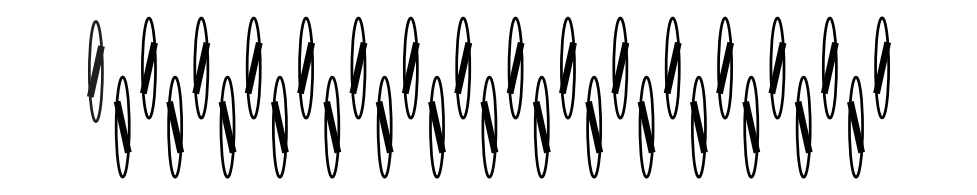

```mathematica
Graphics[primitivesList]
```

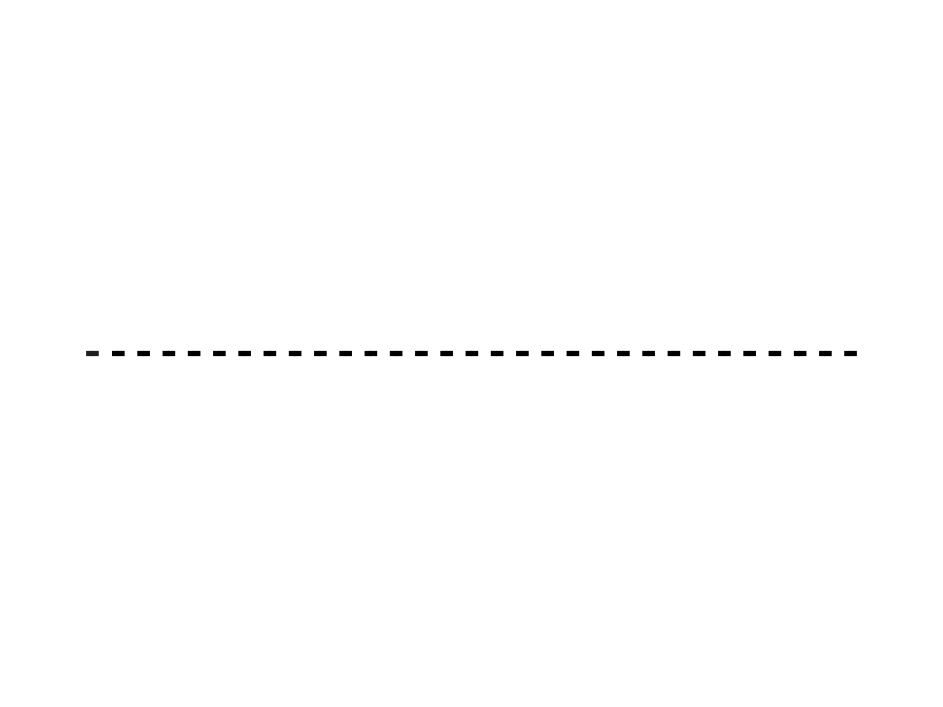

```mathematica
arrowSize=30;
fcolor=GrayLevel[(arrowSize-#)/arrowSize]&;
Graphics[MapThread[{fcolor[Norm@#2],Thickness[0.004],Arrowheads[.01],Arrow[{{#1-Sign[#2]arrowSize/2,0},{#1+Sign[#2]arrowSize/2,0}}]}&,fieldData[[All,{1,3}]]ᵀ]]
```

### Validation: evolution of local responses

```mathematica
h=Normal[WeightedAdjacencyMatrix[graphPert]];
c=chiralList[graphPert];
pA=(ConstantArray[1,Length@c]+c)/2;
pB=(ConstantArray[1,Length@c]-c)/2;
```

#### Initial conditions

```mathematica
{{negEval,negEvec},{zmEval,zmEvec}}=negativeAndZMspectrum[h,0.01];
{localBasis,accuracyList}=localizedBasisPencilMatrix[graphPert,negEvec,0.9];

icWannier=localBasis[[Ceiling[nRotors/2]-1]];
icDelta=Normalize@Normal@SparseArray[{2Ceiling[nRotors/2]-1->1},2(nRotors+1)-1];
icGaussian=Normalize@Chop[Quiet@With[{σ=0.2},ⅇ^((-(Ceiling[nRotors/2]-0.5-0.5 #)^2)/σ)&/@Range[2(nRotors+1)-1]]];
icList={icWannier,icDelta,icGaussian};
```

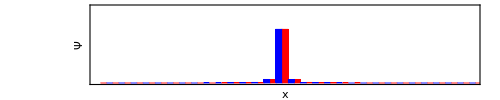
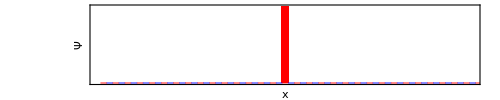
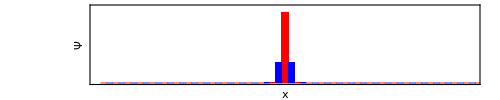

```mathematica
Show[BarChart[#,ChartStyle->{Red,Blue},AspectRatio->0.2,BarOrigin->Bottom,PlotRange->{{0,2nRotors},{0,1.}},FrameTicks->None,AxesLabel->{"x","Ψ"},ImageSize->500,Frame->True]&/@{Abs@(pA #),Abs@(pB #)}&@(#)]&/@icList
```

#### Time evolution

```mathematica
tf=29.9;(*40;*)
dt=0.1;
solList={solWannier,solDelta,solGaussian}=NDSolve[{ⅈ x'[t]==-(h).x[t],x[0]==#},x,{t,0,tf}]&/@icList;
solTable=Table[(x[#]/.sol[[1]])&/@Range[0,tf,dt],{sol,solList}];
```

```mathematica
solTable[[1]]//Dimensions
```

{300,63}

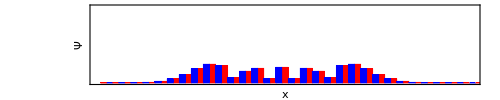
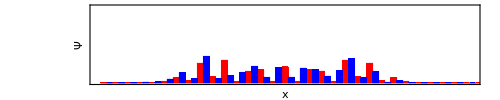
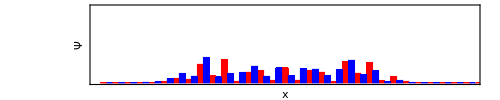

```mathematica
Show[BarChart[#,ChartStyle->{Red,Blue},AspectRatio->0.2,BarOrigin->Bottom,PlotRange->{{0,2nRotors},{0,1.}},FrameTicks->None,AxesLabel->{"x","Ψ"},ImageSize->500,Frame->True]&/@{Abs@(pA #),Abs@(pB #)}&@(#)]&/@(solTable[[All,-1,All]])
```

#### Correlations

Example: we expect dataA and dataB to be correlated, while A and C uncorrelated. (BC uncorrelated as well)

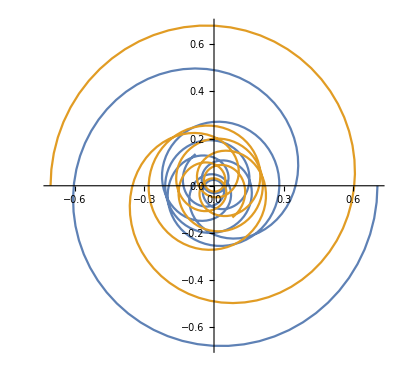

```mathematica
ComplexListPlot[{dataA,dataB},Joined->True]
```

```mathematica
dataA=solTable[[3,All,29]];
dataB=solTable[[3,All,30]];
dataC=solTable[[3,All,28]];
meanA=Mean@dataA;
meanB=Mean@dataB;
meanC=Mean@dataC;
```

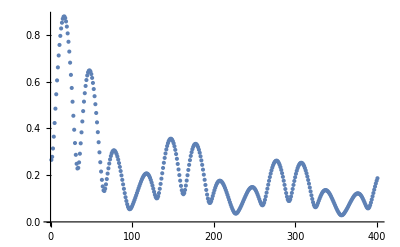

```mathematica
ListPlot[Abs@dataA,PlotRange->All]
```

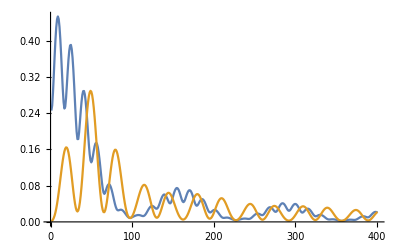

```mathematica
ListPlot[{Abs[dataA]Abs[dataB],Abs[dataA]Abs[dataC]},PlotRange->All,Joined->True]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

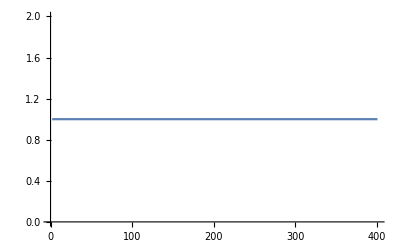

```mathematica
ListPlot[MapThread[(#1 #2*)/(Sqrt[(#1#1*)]Sqrt[(#2 #2*)])&,{Abs@dataA,Abs@dataC}],Joined->True,PlotRange->All]
```

```mathematica
corrTableAA=Table[dt Sum[dataA[[i]]dataA[[i+j]],{i,1,tf/dt-j}]-meanA meanA,{j,0,tf/dt}];
corrTableAB=Table[dt Sum[dataA[[i]]dataB[[i+j]],{i,1,tf/dt-j}]-meanA meanB,{j,0,tf/dt}];
corrTableAC=Table[dt Sum[dataA[[i]]dataC[[i+j]],{i,1,tf/dt-j}]-meanA meanC,{j,0,tf/dt}];
corrTableBC=Table[dt Sum[dataB[[i]]dataC[[i+j]],{i,1,tf/dt-j}]-meanB meanC,{j,0,tf/dt}];
```

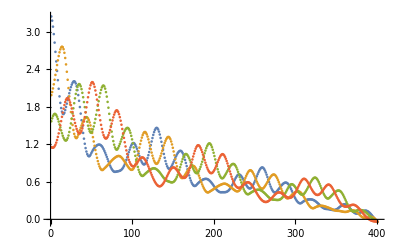

```mathematica
ListPlot[{corrTableAA,corrTableAB,corrTableAC,corrTableBC}]
```

```mathematica
Mean[dataA-Mean[dataA]]/StandardDeviation[dataA] Mean[dataB-Mean[dataB]]/StandardDeviation[dataB]
```

1.17559×10^-33

```mathematica
ListPlot[Mean[dataA-Mean[dataA]],PlotRange->All]
```

ListPlot::lpn: -4.49903×10^-18 is not a list of numbers or pairs of numbers.

ListPlot[-4.49903×10^-18,PlotRange→All]

```mathematica
A
```

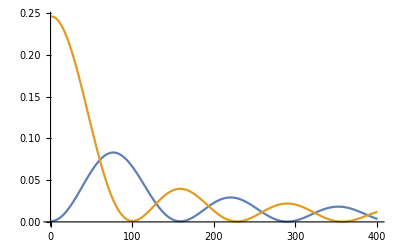

```mathematica
ListPlot[Table[{Abs[solTable[[1,1,29]]]^2 Abs[solTable[[1,1+i,28]]]^2,Abs[solTable[[1,1,29]]]^2 Abs[solTable[[1,1+i,30]]]^2},{i,0,tf/dt}]ᵀ,Joined->True,PlotRange->All]
```

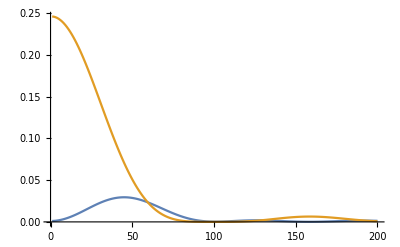
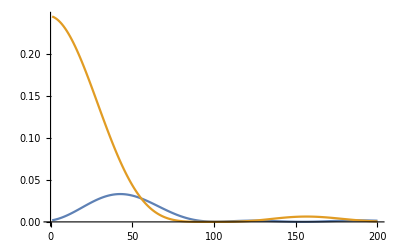
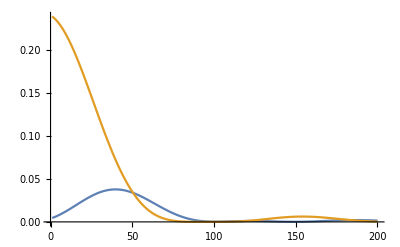
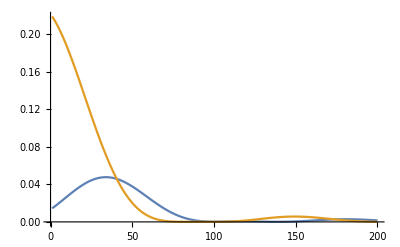
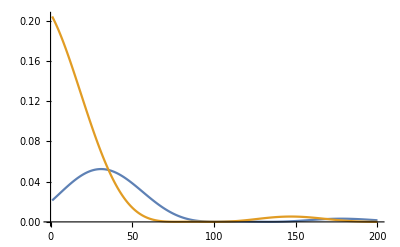
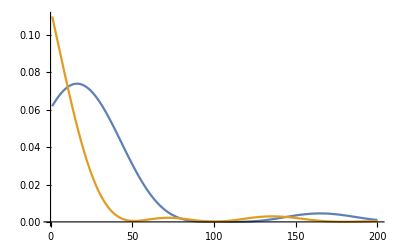

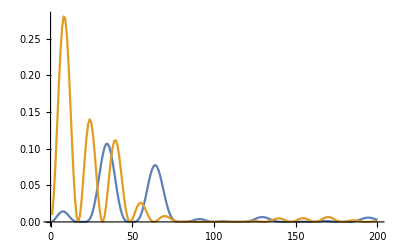
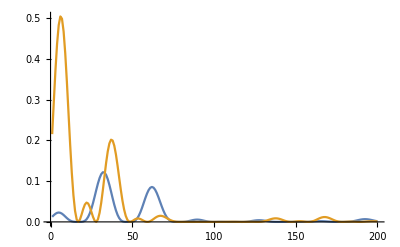

```mathematica
Table[ListPlot[Table[{Abs[solTable[[1,i,29]]]^2 Abs[solTable[[1,j+i,28]]]^2,Abs[solTable[[1,i,29]]]^2 Abs[solTable[[1,i+j,30]]]^2},{i,1,200}]ᵀ,Joined->True,PlotRange->All],{j,{1,5,10,20,25,50}}]
Table[ListPlot[Table[{Abs[solTable[[2,i,29]]]^2 Abs[solTable[[2,j+i,28]]]^2,Abs[solTable[[2,i,29]]]^2 Abs[solTable[[2,i+j,30]]]^2},{i,1,200}]ᵀ,Joined->True,PlotRange->All],{j,{1,5,10,20,25,50}}]
Table[ListPlot[Table[{Abs[solTable[[3,i,29]]]^2 Abs[solTable[[3,j+i,28]]]^2,Abs[solTable[[3,i,29]]]^2 Abs[solTable[[3,i+j,30]]]^2},{i,1,200}]ᵀ,Joined->True,PlotRange->All],{j,{1,5,10,20,25,50}}]
```

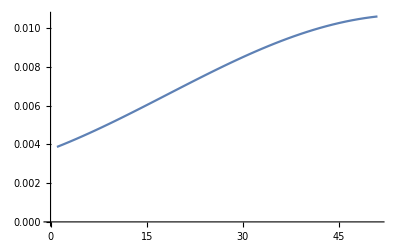

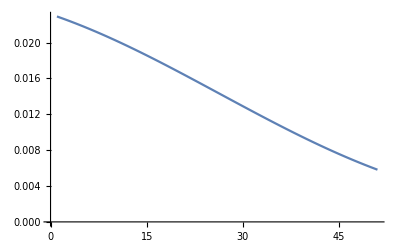

```mathematica
ListPlot[Table[Mean@Table[Abs[solTable[[1,i,29]]]^2 Abs[solTable[[1,j+i,28]]]^2,{i,1,tf/dt-j}],{j,0,50}],Joined->True]
ListPlot[Table[Mean@Table[Abs[solTable[[1,i,29]]]^2 Abs[solTable[[1,j+i,30]]]^2,{i,1,tf/dt-j}],{j,0,50}],Joined->True]
```

```mathematica
Table[ListPlot[Table[{Abs[solTable[[1,i,29]]]^2 Abs[solTable[[1,j+i,28]]]^2,Abs[solTable[[1,i,29]]]^2 Abs[solTable[[1,i+j,30]]]^2},{i,1,200}]ᵀ,Joined->True,PlotRange->All],{j,{1,5,10,20,25,50}}]
```

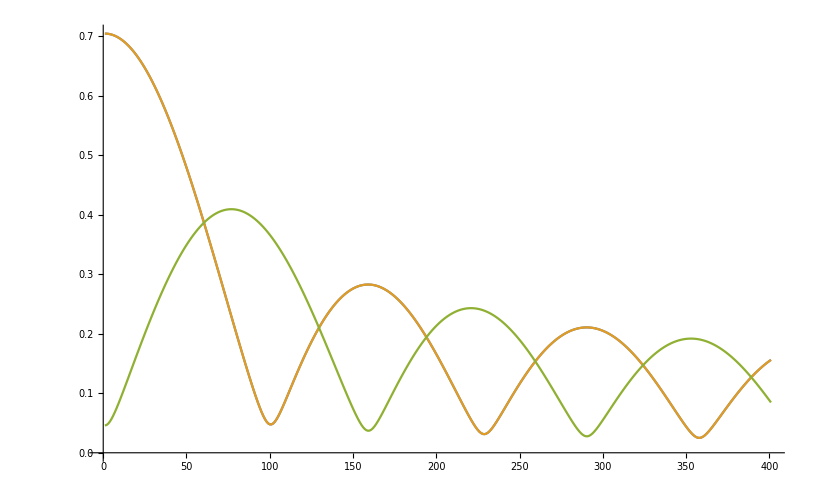

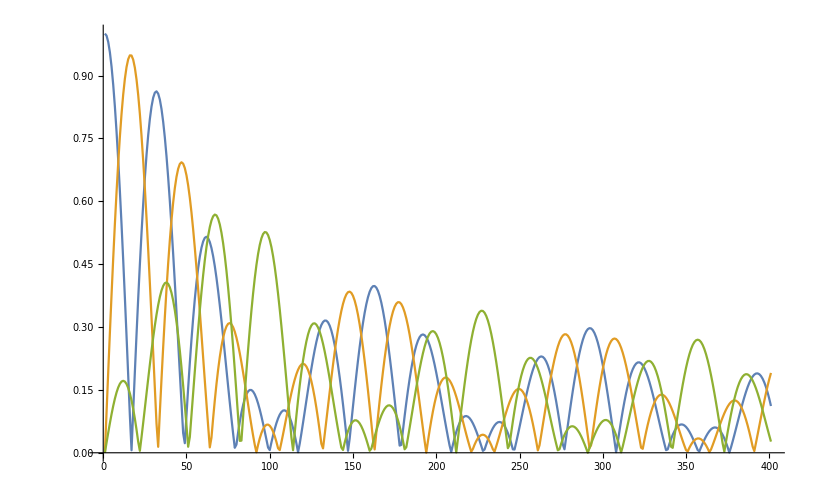

```mathematica
ListPlot[{Abs@solTable[[1,All,29]],Abs@solTable[[1,All,30]],Abs@solTable[[1,All,28]]},Joined->True]
ListPlot[{Abs@solTable[[2,All,29]],Abs@solTable[[2,All,30]],Abs@solTable[[2,All,28]]},PlotRange->All,Joined->True]
```

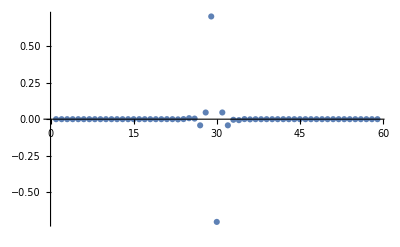

```mathematica
ListPlot[solTable[[1,1]],PlotRange->All]
```

#### Velocity correlation

```mathematica
dataA=Abs@solTable[[1,All,29]];
dataB=Abs@solTable[[1,All,30]];
dataC=Abs@solTable[[1,All,28]];
velDataA=dataA[[2;;]]-dataA[[;;-2]];
velDataB=dataB[[2;;]]-dataB[[;;-2]];
velDataC=dataC[[2;;]]-dataC[[;;-2]];
```

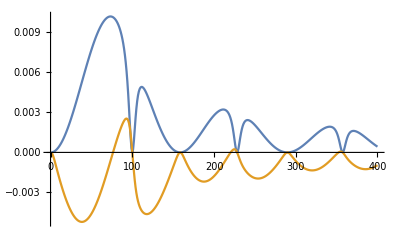

```mathematica
ListPlot[{(velDataA velDataB)/(Norm@velDataA Norm@velDataB),(velDataA velDataC)/(Norm@velDataB Norm@velDataC)},PlotRange->All,Joined->True]
```

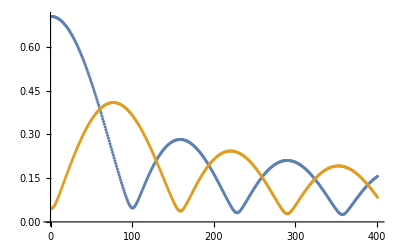

```mathematica
ListPlot[{Abs[dataA],Abs@dataC}]
```

#### Spatial correlation

```mathematica
ListPlot3D[Abs@solTable[[#]]]&/@{1,2,3}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
dataWannier=solTable[[1]];
```

```mathematica
dataWannier//Dimensions
```

{401,59}

```mathematica
aer=Table[Abs[dataWannier[[j,2i]]]Abs[dataWannier[[j,2i+1]]],{i,1,25},{j,1,200}];
aer2=Table[Abs[dataWannier[[j,2i]]]Abs[dataWannier[[j,2i-1]]],{i,1,25},{j,1,200}];
aer3=Table[Abs[dataWannier[[j,2i]]](Abs[dataWannier[[j,2i+1]]]-Abs[dataWannier[[j,2i-1]]]),{i,1,25},{j,1,200}];
```

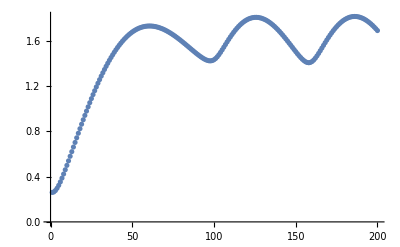

```mathematica
ListPlot[Total[aer]/(Total[Table[Abs[dataWannier[[j,2i]]]Abs[dataWannier[[j,2i]]],{i,1,25},{j,1,200}]]Total[Table[Abs[dataWannier[[j,2i+1]]]Abs[dataWannier[[j,2i+1]]],{i,1,25},{j,1,200}]])]
```

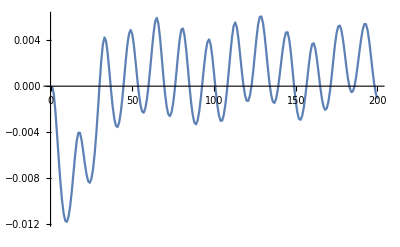

```mathematica
ListPlot[Mean@aer3,Joined->True,PlotRange->All]
```

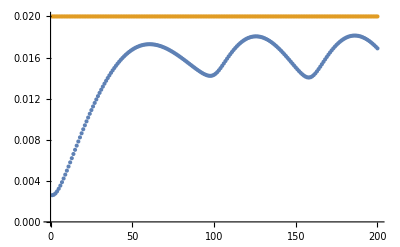

```mathematica
ListPlot[{Mean[aer],Mean[aer2]}]
```

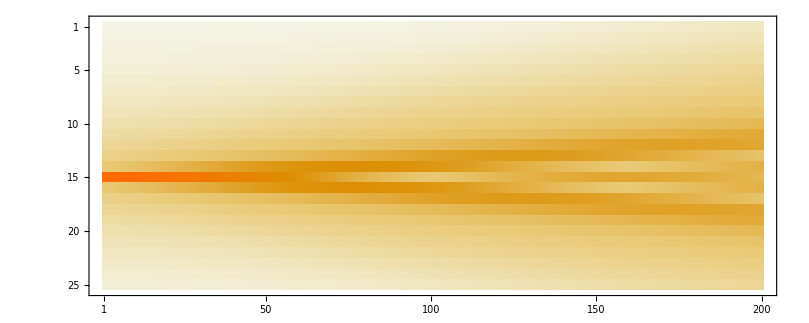

```mathematica
MatrixPlot@aer2
```

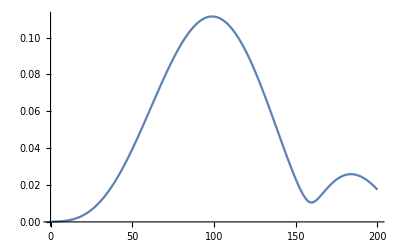

```mathematica
ListPlot[aer[[13]],Joined->True,PlotRange->All]
```

#### Moments

```mathematica
positions=positionList[graphPert]/(unitcellLength);
momentsList=(Quiet@Map[With[{norm2=(#*.#)},
{
Sqrt[norm2],
(#*.(c#))/norm2,
1/norm2(#*.(positions[[All,1]]#)),
1/norm2(#*.(positions[[All,2]]#)),
1/norm2(#*.(c positions[[All,1]]#)),
1/norm2(#*.(c positions[[All,2]]#))
}]&,#])&/@solTable;
```

```mathematica
fieldData=Map[{#[[3]],#[[4]],2(#[[5]]-#[[2]]#[[3]]),2(#[[6]]-#[[2]]#[[4]])}&,#]&/@momentsList;
```

```mathematica
absData=Abs[#ᵀ]&/@solTable;
xpositions=positions[[All,1]];
absData=Flatten[Table[{xpositions[[i]],dt(j-1),#[[i,j]]},{i,1,2nRotors-1},{j,1,1+tf/dt}],1]&/@absData;
```

```mathematica
cf2=Blend[{{0,White},{1.,Black}},#]&;
densityPlotList=ListDensityPlot[#,ColorFunction->cf2,PlotRange->All,ScalingFunctions->{Identity,"Reverse"},PlotRangePadding->0,FrameTicks->None]&/@absData;
```

```mathematica
colorList={Black,Orange,Darker[Green]};
optionsListPlot={Joined->True,Frame->True,PlotRange->All,GridLines->Automatic,PlotStyle->colorList};
```

```mathematica
tRange=Range[0,tf,dt];
```

```mathematica
centerTrajectoryListPlot=MapThread[ListPlot[{#1,tRange}ᵀ,Joined->True,ScalingFunctions->{Identity,"Reverse"},PlotStyle->{{Thickness[0.01],#2}},Ticks->None]&,{(fieldData[[All,All,1]]),colorList}];
```

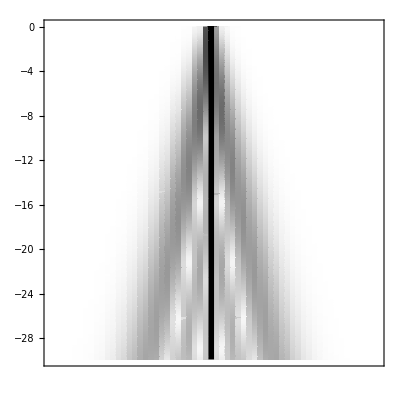
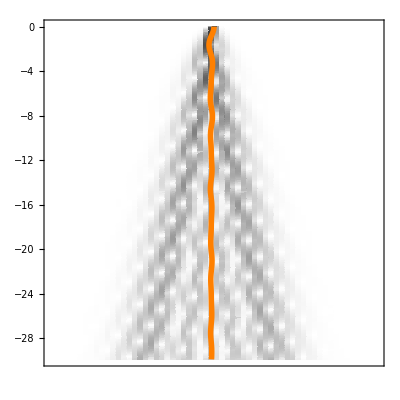
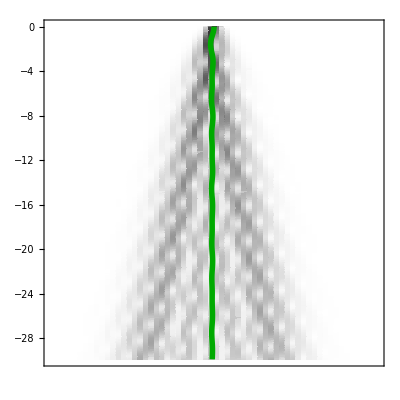

```mathematica
MapThread[Show[{#1,#2}]&,{densityPlotList,centerTrajectoryListPlot}]
```

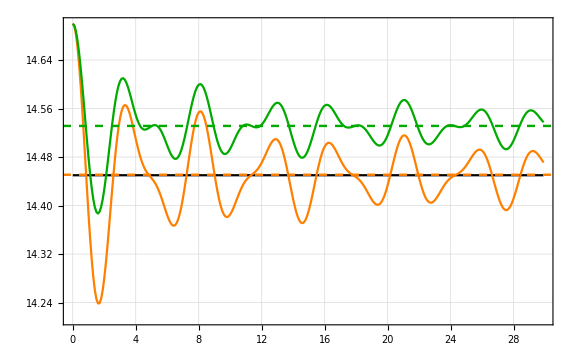

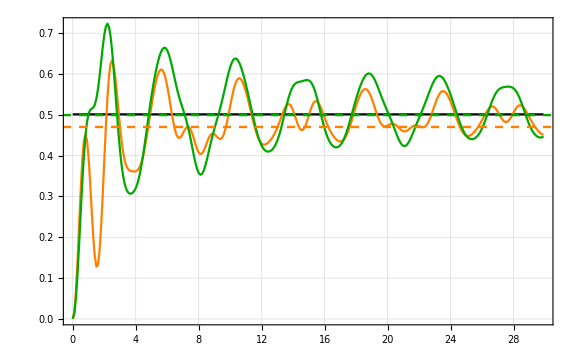

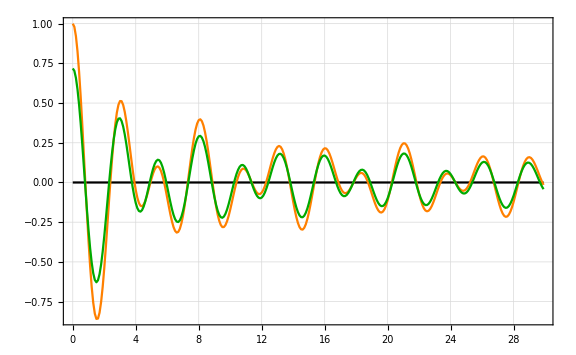

```mathematica
ListPlot[{tRange,#}ᵀ&/@(fieldData[[All,All,1]]),Evaluate[optionsListPlot],Epilog->{colorList[[2]],Dashing[0.01],Thickness[0.003],InfiniteLine[{{0,Mean[fieldData[[2,All,1]]]},{10,Mean[fieldData[[2,All,1]]]}}],colorList[[3]],InfiniteLine[{{0,Mean[fieldData[[3,All,1]]]},{10,Mean[fieldData[[3,All,1]]]}}]}]
ListPlot[{tRange,#}ᵀ&/@(fieldData[[All,All,3]]),Evaluate[optionsListPlot],Epilog->{colorList[[2]],Dashing[0.01],Thickness[0.003],InfiniteLine[{{0,Mean[fieldData[[2,All,3]]]},{10,Mean[fieldData[[2,All,3]]]}}],colorList[[3]],InfiniteLine[{{0,Mean[fieldData[[3,All,3]]]},{10,Mean[fieldData[[3,All,3]]]}}]}]
ListPlot[{tRange,#}ᵀ&/@(momentsList[[All,All,2]]),Evaluate[optionsListPlot]]
```

Plots shown independently

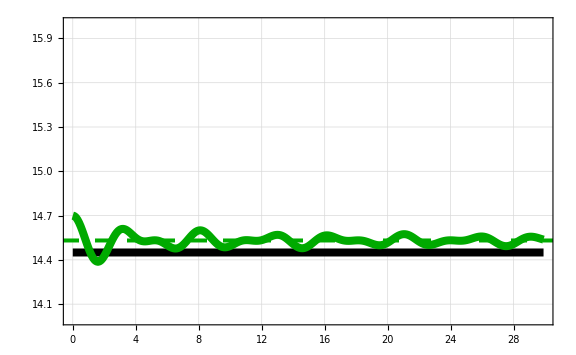

```mathematica
indices={1,3};
pRange={{0,tf},{14,16}};
optionsListPlot={PlotRange->pRange,Joined->True,Frame->True,GridLines->Automatic,ImageSize->Large};
ListPlot[{tRange,#}ᵀ&/@(fieldData[[indices,All,1]]),PlotStyle->({Thickness[0.01],#}&/@(colorList[[indices]])),Epilog->{colorList[[indices[[2]]]],Dashing[0.02],Thickness[0.005],InfiniteLine[{{0,Mean[fieldData[[indices[[2]],All,1]]]},{10,Mean[fieldData[[indices[[2]],All,1]]]}}]},
Evaluate[optionsListPlot],FrameStyle->Directive[Black,FontSize->30],GridLinesStyle->Thickness[0.002]]
```

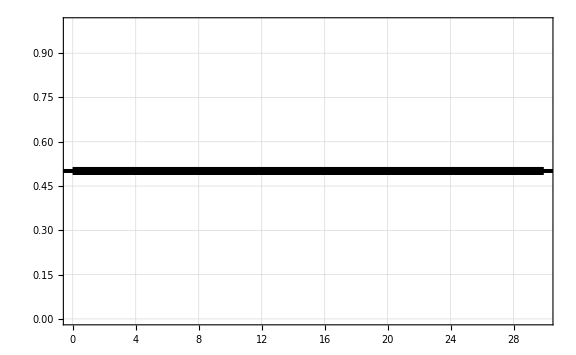

```mathematica
indices={1,1};
pRange={{0,tf},{0,1}};
optionsListPlot={PlotRange->pRange,Joined->True,Frame->True,GridLines->Automatic,ImageSize->Large};
ListPlot[{tRange,#}ᵀ&/@(fieldData[[indices,All,3]]),PlotStyle->({Thickness[0.01],#}&/@(colorList[[indices]])),Epilog->{colorList[[indices[[2]]]],Dashing[0.02],Thickness[0.005],InfiniteLine[{{0,Mean[fieldData[[indices[[2]],All,3]]]},{10,Mean[fieldData[[indices[[2]],All,3]]]}}]},
Evaluate[optionsListPlot],FrameStyle->Directive[Black,FontSize->30],GridLinesStyle->Thickness[0.002]]
```

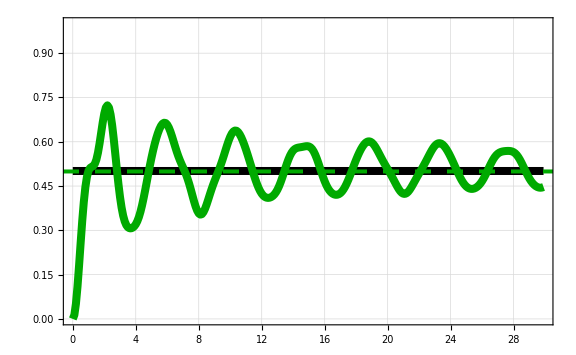

```mathematica
indices={1,3};
pRange={{0,tf},{0,1}};
optionsListPlot={PlotRange->pRange,Joined->True,Frame->True,GridLines->Automatic,ImageSize->Large};
ListPlot[{tRange,#}ᵀ&/@(fieldData[[indices,All,3]]),PlotStyle->({Thickness[0.01],#}&/@(colorList[[indices]])),Epilog->{colorList[[indices[[2]]]],Dashing[0.02],Thickness[0.005],InfiniteLine[{{0,Mean[fieldData[[indices[[2]],All,3]]]},{10,Mean[fieldData[[indices[[2]],All,3]]]}}]},
Evaluate[optionsListPlot],FrameStyle->Directive[Black,FontSize->30],GridLinesStyle->Thickness[0.002]]
```

### Validation: comparison with FEM simulations

```mathematica
(*data obtained from mechanical SSH - minimal.nb with data from FEM4*)
distFEM={};
```

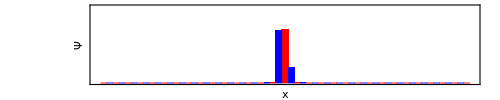

```mathematica
Show[BarChart[#,ChartStyle->{Red,Blue},AspectRatio->0.2,BarOrigin->Bottom,PlotRange->{{0,2nRotors},{0,1.}},FrameTicks->None,AxesLabel->{"x","Ψ"},ImageSize->500,Frame->True]&/@{Abs@(pA[[;;-3]] #),Abs@(pB[[;;-3]] #)}&@(distFEM[[1]])]
```

#### Moments

```mathematica
positions=positionList[graphPert][[;;-3]]/(unitcellLength);
c=chiralList[graphPert][[;;-3]];
rightIndices={2,1}~Join~Range[3,61];
positions=positions[[rightIndices]];
c=c[[rightIndices]];
momentsList=(Quiet@Map[With[{norm2=(#*.#)},
{
Sqrt[norm2],
(#*.(c#))/norm2,
1/norm2(#*.(positions[[All,1]]#)),
1/norm2(#*.(positions[[All,2]]#)),
1/norm2(#*.(c positions[[All,1]]#)),
1/norm2(#*.(c positions[[All,2]]#))
}]&,#])&/@{distFEM};
```

```mathematica
fieldData=Map[{#[[3]],#[[4]],2(#[[5]]-#[[2]]#[[3]]),2(#[[6]]-#[[2]]#[[4]])}&,#]&/@momentsList;
```

```mathematica
absData=Abs[#ᵀ]&/@{distFEM};
xpositions=positions[[All,1]];
absData=Flatten[Table[{xpositions[[i]],dt(j-1),#[[i,j]]},{i,1,2nRotors-1},{j,1,Length@distFEM}],1]&/@absData;
```

```mathematica
cf2=Blend[{{0,White},{1.,Black}},#]&;
densityPlotList=ListDensityPlot[#,ColorFunction->cf2,PlotRange->All,ScalingFunctions->{Identity,"Reverse"},PlotRangePadding->0,FrameTicks->None]&/@absData;
```

```mathematica
colorList={Black,Orange,Darker[Green]};
optionsListPlot={Joined->True,Frame->True,PlotRange->All,GridLines->Automatic,PlotStyle->colorList};
```

```mathematica
tRange=Range[0,dt (Length[distFEM]-1),dt];
```

```mathematica
colorList={ColorData["Rainbow"][0.75]};
```

```mathematica
centerTrajectoryListPlot=MapThread[ListPlot[{#1,tRange}ᵀ,Joined->True,ScalingFunctions->{Identity,"Reverse"},PlotStyle->{{Thickness[0.01],#2}},Ticks->None]&,{(fieldData[[All,All,1]]),colorList}];
```

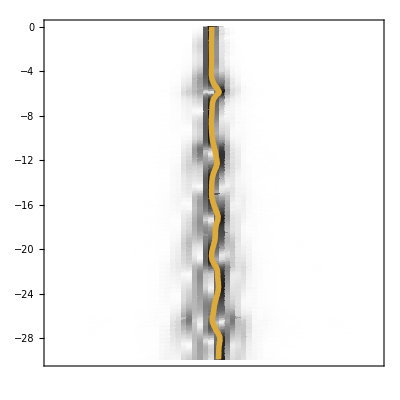

```mathematica
MapThread[Show[{#1,#2}]&,{densityPlotList,centerTrajectoryListPlot}]
```

Plots shown independently

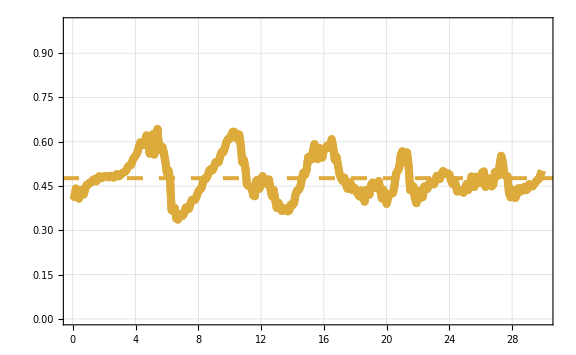

```mathematica
indices={1,1};
pRange={{0,dt Length[distFEM]},{0,1}};
optionsListPlot={PlotRange->pRange,Joined->True,Frame->True,GridLines->Automatic,ImageSize->Large};
ListPlot[{tRange,#}ᵀ&/@(fieldData[[indices,All,3]]),PlotStyle->({Thickness[0.01],#}&/@(colorList[[indices]])),Epilog->{colorList[[indices[[2]]]],Dashing[0.02],Thickness[0.005],InfiniteLine[{{0,Mean[fieldData[[indices[[1]],All,3]]]},{10,Mean[fieldData[[indices[[1]],All,3]]]}}]},
Evaluate[optionsListPlot],FrameStyle->Directive[Black,FontSize->30],GridLinesStyle->Thickness[0.002]]
```

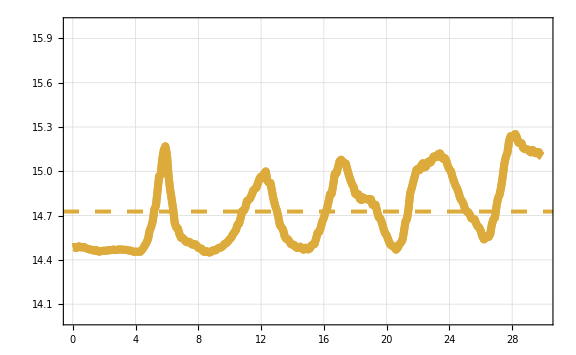

```mathematica
indices={1,1};
pRange={{0,dt Length[distFEM]},{14,16}};
optionsListPlot={PlotRange->pRange,Joined->True,Frame->True,GridLines->Automatic,ImageSize->Large};
ListPlot[{tRange,#}ᵀ&/@(fieldData[[indices,All,1]]),PlotStyle->({Thickness[0.01],#}&/@(colorList[[indices]])),Epilog->{colorList[[indices[[2]]]],Dashing[0.02],Thickness[0.005],InfiniteLine[{{0,Mean[fieldData[[indices[[2]],All,1]]]},{10,Mean[fieldData[[indices[[2]],All,1]]]}}]},
Evaluate[optionsListPlot],FrameStyle->Directive[Black,FontSize->30],GridLinesStyle->Thickness[0.002]]
```

```mathematica
indices={1,2};
pRange={{0,tf},{0,1}};
optionsListPlot={PlotRange->pRange,Joined->True,Frame->True,GridLines->Automatic,ImageSize->Large};
ListPlot[{tRange,#}ᵀ&/@(fieldData[[indices,All,3]]),PlotStyle->({Thickness[0.01],#}&/@(colorList[[indices]])),Epilog->{colorList[[indices[[2]]]],Dashing[0.02],Thickness[0.005],InfiniteLine[{{0,Mean[fieldData[[indices[[2]],All,3]]]},{10,Mean[fieldData[[indices[[2]],All,3]]]}}]},
Evaluate[optionsListPlot],FrameStyle->Directive[Black,FontSize->30],GridLinesStyle->Thickness[0.002]]
```

Part::partw: Part {1,2} of {{{14.4849,0.146378,0.419897,0.299811},{14.4872,0.145452,0.413021,0.299562},{14.4803,0.149468,0.441685,0.29881},«6»,{14.4768,0.153728,0.454708,0.294894},«290»}} does not exist.

Transpose::nmtx: The first two levels of {{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,«290»},{{{14.4849,0.146378,0.419897,0.299811},{14.4872,0.145452,0.413021,0.299562},«7»,{14.4768,0.153728,0.454708,0.294894},«290»}}} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,«290»},{1,2}} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,«290»},All} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::pkspec1: The expression Transpose[{{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,«290»},{1,2}}] cannot be used as a part specification.

Part::partw: Part {1,2} of {color} does not exist.

Part::pkspec1: The expression {Thickness[0.01],{1,2}} cannot be used as a part specification.

Part::partw: Part 2 of {color} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: Transpose[{{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,«290»},{{{14.4849,0.146378,0.419897,0.299811},{14.4872,0.145452,0.413021,0.299562},«7»,{14.4768,0.153728,0.454708,0.294894},«290»}}}]⟦Transpose[«1»],«1»,«1»⟧ is not a list of numbers or pairs of numbers.

## Domain wall: FM

```mathematica
(*Model dependent part*)
Clear[keysBeadsUC,pairKeysUC,posBeadsUC,identityUC,translationOp,posPivotsUC];
{keysBeadsUC[i_],pairKeysUC[i_],identityUC,posBeadsUC,translationOp[i_],posPivotsUC}=Module[{keysBeads,posBeads,pairKeys,identity,l={i},pVec1,pVec2,transOp,posPivots,recBasis},
Clear[a,b];
(*definition of beads and connectivity*)
keysBeads=#@@l&/@{a,b};
pairKeys={{a@@l,b@@l},{b@@l,a@@(l+1)}};

(*primitive vectors and positions*)
pVec1=2{unitcellLength,0};
transOp={pVec1}(i-1);
posPivots={{0,0},pVec1/2};
posBeads=Table[posPivots[[i]]+radius AngleVector[(-1)^(i+1)45Degree],{i,1,2}];
identity={1,1};


{keysBeads,pairKeys,identity,posBeads,transOp,posPivots}
];
```

```mathematica
{keysBeads,pairKeysBeads,identity,posBeads,posPivots}=tesselate[{Ceiling[Length@angleListSingleDomain]},keysBeadsUC,pairKeysUC,identityUC,posBeadsUC,translationOp,posPivotsUC];
```

```mathematica
keysBeads={"a[1]","b[1]","a[2]","b[2]","a[3]","b[3]","a[4]","b[4]","a[5]","b[5]","a[6]","b[6]","a[7]"};
pairKeysBeads={{"a[1]","b[1]"},{"b[1]","a[2]"},{"a[2]","b[2]"},{"b[2]","a[3]"},{"a[3]","b[3]"},{"b[3]","a[4]"},{"a[4]","b[4]"},{"b[4]","a[5]"},{"a[5]","b[5]"},{"b[5]","a[6]"},{"a[6]","b[6]"},{"b[6]","a[7]"}};
identity=ConstantArray[1,Length@keysBeads];
```

```mathematica
posPivots=#{unitcellLength,0}&/@Range[0,12];
```

```mathematica
aux=N@((-1)^(#+1))45Degree&/@Range[6];
aux2=N@((-1)^#)135Degree&/@Range[6];
(*aux2=(N@π-#&/@aux)[[1;;-1]];*)
angleListDomainWallFM=N[aux~Join~{π/2}~Join~aux2];
```

```mathematica
angleListDomainWallFM//Dimensions
```

{13}

```mathematica
posBeads=MapThread[#1+radius AngleVector[#2]&,{posPivots,angleListDomainWallFM}];
```

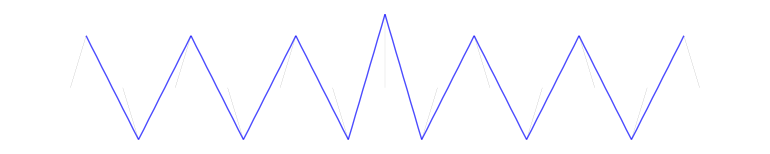

```mathematica
beadAndSpringGraphic2D[{keysBeads,pairKeysBeads,identity,posBeads,posPivots}]
```

```mathematica
graphBeads=eqSystem[keysBeads,pairKeysBeads,AssociationThread[keysBeads,posBeads]];
graphPert=pertSystem[graphBeads,AssociationThread[keysBeads,identity],AssociationThread[keysBeads,posBeads],AssociationThread[keysBeads,posPivots]];
```

### Finite system

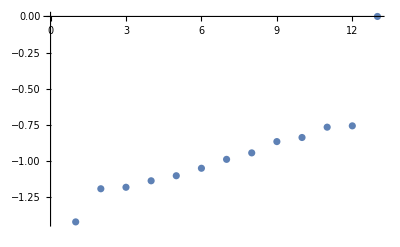

```mathematica
{{negEval,negEvec},{zmEval,zmEvec}}=negativeAndZMspectrum[Normal[WeightedAdjacencyMatrix[graphPert]],0.01];
{projA,projB}={projAList[#],projBList[#]}&@graphPert;
ListPlot[negEval~Join~zmEval]
```

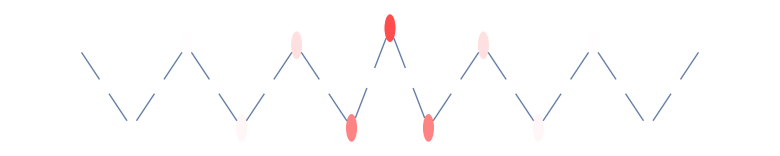

```mathematica
highlightGraph[Graph[graphPert,VertexSize->0.4],Total[zmEvec^2]^(1/2),0]
```

```mathematica
{localBasis,accuracyList}=localizedBasisPencilMatrix[graphPert,negEvec,0.9];
```

#### Visualization of Wannier functions

```mathematica
positions=positionList[graphPert];
```

```mathematica
nWannier=7;
data={positions[[All,1]],localBasis[[nWannier]]}ᵀ;
```

```mathematica
colorList=If[#==-1,Blue,Red]&/@chiralList[graphPert];
```

```mathematica
positions
```

{{48.,0.},{18.,18.},{78.,-18.},{108.,0.},{138.,18.},{168.,0.},{198.,-18.},{228.,0.},{258.,18.},{288.,0.},{318.,-18.},{348.,0.},{378.,18.},{408.,0.},{438.,-18.},{468.,0.},{498.,18.},{528.,0.},{558.,-18.},{588.,0.},{618.,18.},{648.,0.},{678.,-18.},{708.,0.},{738.,18.},{768.,0.},{798.,-18.}}

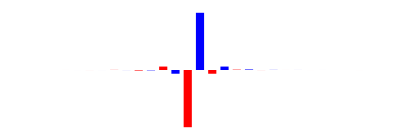

```mathematica
width=20;
amplificationFactor=200;
Graphics[MapThread[{#2,Rectangle[{#[[1]]-width/2,0},{#[[1]]+width/2,amplificationFactor#[[2]]}]}&,{data,colorList}]]
```

```mathematica
localBasis[[7]]//Dimensions
```

{27}

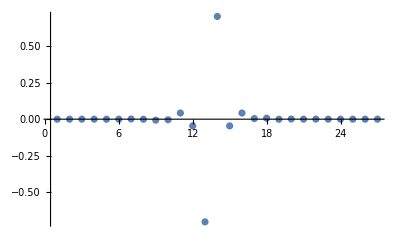

```mathematica
ListPlot[localBasis[[7]],PlotRange->All]
```

#### Chiral polarization field

```mathematica
positions=positionList[graphPert];
chiral=chiralList[graphPert];
```

```mathematica
momentsList=Quiet@Map[With[{norm2=(#*.#)},
{
Sqrt[norm2],
(#*.(chiral#))/norm2,
1/norm2(#*.(positions[[All,1]]#)),
1/norm2(#*.(positions[[All,2]]#)),
1/norm2(#*.(chiral positions[[All,1]]#)),
1/norm2(#*.(chiral positions[[All,2]]#))
}]&,localBasis];
```

```mathematica
fieldData=Map[{#[[3]],#[[4]],2(#[[5]]-#[[2]]#[[3]]),2(#[[6]]-#[[2]]#[[4]])}&,momentsList];
```

```mathematica
fcolor=GrayLevel[(35-#)/35]&;
barl=BarLegend[{fcolor[#]&,{0,40}},LegendLabel->"Norm",LabelStyle->Directive[Black,FontSize->14]];
primitivesList=Map[Module[{center={#1[[1]],#1[[2]]},pol={#1[[3]],#1[[4]]},unitvector,norm,circleRadius=15},
norm=Norm@pol;
unitvector=Normalize[pol];
{fcolor[norm],Thickness[0.005],Arrowheads[.02],Arrow[{center-unitvector circleRadius,center+unitvector circleRadius}],Thickness[0.002],Circle[center,circleRadius]}
]&,fieldData];
```

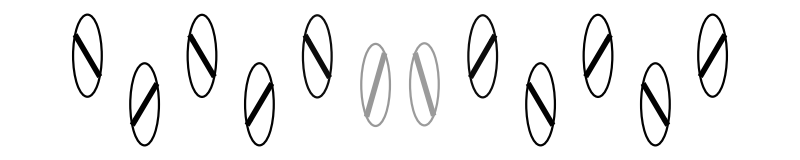

```mathematica
Graphics[primitivesList]
```

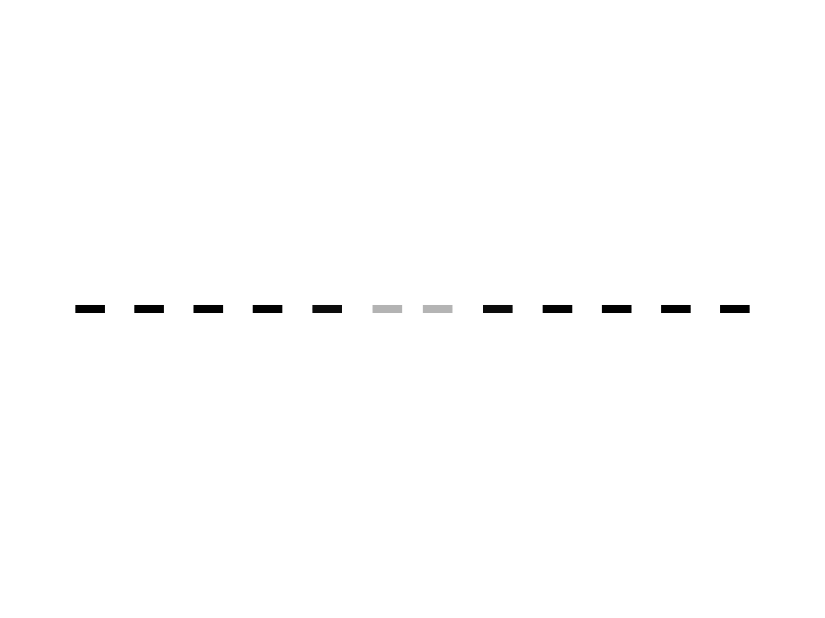

```mathematica
arrowSize=30;
fcolor=GrayLevel[(arrowSize-#)/arrowSize]&;
Graphics[MapThread[{fcolor[Norm@#2],Thickness[0.007],Arrowheads[.03],Arrow[{{#1-Sign[#2]arrowSize/2,0},{#1+Sign[#2]arrowSize/2,0}}]}&,fieldData[[All,{1,3}]]ᵀ]]
```

## Domain wall: SSS

```mathematica
{keysBeads,pairKeysBeads,identity,posBeads,posPivots}=tesselate[{Ceiling[Length@angleListSingleDomain]},keysBeadsUC,pairKeysUC,identityUC,posBeadsUC,translationOp,posPivotsUC];
```

```mathematica
keysBeads={"a[1]","b[1]","a[2]","b[2]","a[3]","b[3]","a[4]","b[4]","a[5]","b[5]","a[6]","b[6]","a[7]"};
pairKeysBeads={{"a[1]","b[1]"},{"b[1]","a[2]"},{"a[2]","b[2]"},{"b[2]","a[3]"},{"a[3]","b[3]"},{"b[3]","a[4]"},{"a[4]","b[4]"},{"b[4]","a[5]"},{"a[5]","b[5]"},{"b[5]","a[6]"},{"a[6]","b[6]"},{"b[6]","a[7]"}};
identity=ConstantArray[1,Length@keysBeads];
```

```mathematica
posPivots=#{unitcellLength,0}&/@Range[0,12];
```

```mathematica
aux=N@((-1)^#)45Degree&/@Range[6];
aux2=N@((-1)^(#+1))135Degree&/@Range[6];
(*aux2=(N@π-#&/@aux)[[1;;-1]];*)
angleListDomainWallFM=N[aux2~Join~{π/2}~Join~aux];
```

```mathematica
posBeads=MapThread[#1+radius AngleVector[#2]&,{posPivots,angleListDomainWallFM}];
```

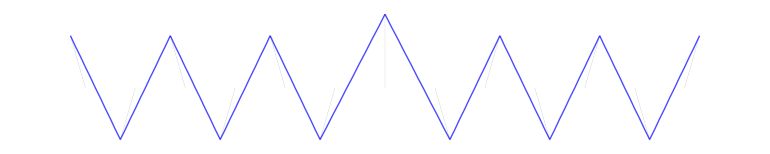

```mathematica
beadAndSpringGraphic2D[{keysBeads,pairKeysBeads,identity,posBeads,posPivots}]
```

```mathematica
graphBeads=eqSystem[keysBeads,pairKeysBeads,AssociationThread[keysBeads,posBeads]];
graphPert=pertSystem[graphBeads,AssociationThread[keysBeads,identity],AssociationThread[keysBeads,posBeads],AssociationThread[keysBeads,posPivots]];
```

### Finite system

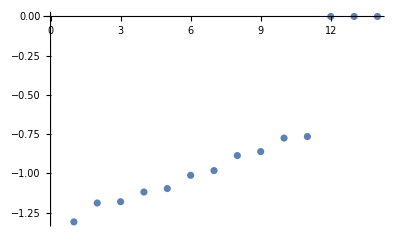

```mathematica
{{negEval,negEvec},{zmEval,zmEvec}}=negativeAndZMspectrum[Normal[WeightedAdjacencyMatrix[graphPert]],0.01];
{projA,projB}={projAList[#],projBList[#]}&@graphPert;
ListPlot[negEval~Join~zmEval]
```

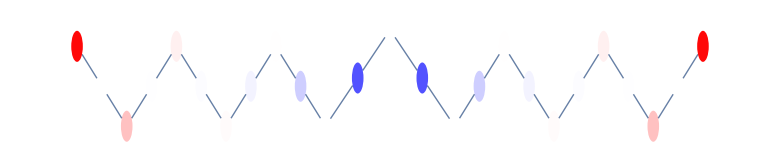

```mathematica
highlightGraph[Graph[graphPert,VertexSize->0.4],Total[zmEvec^2]^(1/2),0]
```

```mathematica
{localBasis,accuracyList}=localizedBasisPencilMatrix[graphPert,negEvec,0.9];
```

#### Visualization of Wannier functions

```mathematica
positions=positionList[graphPert];
```

```mathematica
nWannier=7;
data={positions[[All,1]],localBasis[[nWannier]]}ᵀ;
```

```mathematica
colorList=If[#==-1,Blue,Red]&/@chiralList[graphPert];
```

```mathematica
positions
```

{{48.,0.},{18.,18.},{78.,-18.},{108.,0.},{138.,18.},{168.,0.},{198.,-18.},{228.,0.},{258.,18.},{288.,0.},{318.,-18.},{348.,0.},{378.,18.},{408.,0.},{438.,-18.},{468.,0.},{498.,18.},{528.,0.},{558.,-18.},{588.,0.},{618.,18.},{648.,0.},{678.,-18.},{708.,0.},{738.,18.},{768.,0.},{798.,-18.}}

```mathematica
width=20;
amplificationFactor=200;
Graphics[MapThread[{#2,Rectangle[{#[[1]]-width/2,0},{#[[1]]+width/2,amplificationFactor#[[2]]}]}&,{data,colorList}]]
```

-Graphics-

```mathematica
localBasis[[7]]//Dimensions
```

{27}

```mathematica
ListPlot[localBasis[[7]],PlotRange->All]
```

-Graphics-

#### Chiral polarization field

```mathematica
positions=positionList[graphPert];
chiral=chiralList[graphPert];
```

```mathematica
momentsList=Quiet@Map[With[{norm2=(#*.#)},
{
Sqrt[norm2],
(#*.(chiral#))/norm2,
1/norm2(#*.(positions[[All,1]]#)),
1/norm2(#*.(positions[[All,2]]#)),
1/norm2(#*.(chiral positions[[All,1]]#)),
1/norm2(#*.(chiral positions[[All,2]]#))
}]&,localBasis];
```

```mathematica
fieldData=Map[{#[[3]],#[[4]],2(#[[5]]-#[[2]]#[[3]]),2(#[[6]]-#[[2]]#[[4]])}&,momentsList];
```

```mathematica
fcolor=GrayLevel[(35-#)/35]&;
barl=BarLegend[{fcolor[#]&,{0,40}},LegendLabel->"Norm",LabelStyle->Directive[Black,FontSize->14]];
primitivesList=Map[Module[{center={#1[[1]],#1[[2]]},pol={#1[[3]],#1[[4]]},unitvector,norm,circleRadius=15},
norm=Norm@pol;
unitvector=Normalize[pol];
{fcolor[norm],Thickness[0.005],Arrowheads[.02],Arrow[{center-unitvector circleRadius,center+unitvector circleRadius}],Thickness[0.002],Circle[center,circleRadius]}
]&,fieldData];
```

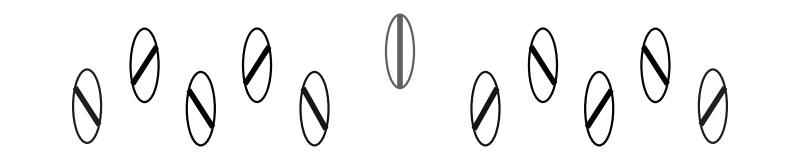

```mathematica
Graphics[primitivesList]
```

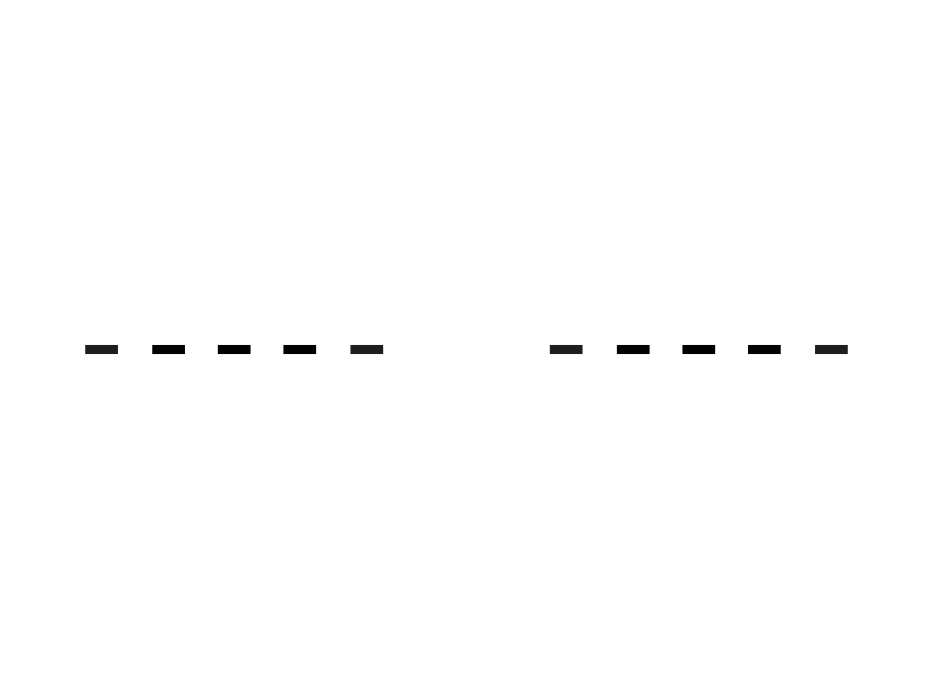

```mathematica
arrowSize=30;
fcolor=GrayLevel[(arrowSize-#)/arrowSize]&;
Graphics[MapThread[{fcolor[Norm@#2],Thickness[0.007],Arrowheads[.03],Arrow[{{#1-Sign[#2]arrowSize/2,0},{#1+Sign[#2]arrowSize/2,0}}]}&,fieldData[[All,{1,3}]]ᵀ]]
```